```mathematica
Quit[]
```

```mathematica
ClearAll["Global`*"]
A1:=+(24 GS lp^2 π p[r]pp)/((r rp)^2 √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))1/(8 GS π ϵ[p[r]]pp)
A2:=-(6 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^5 √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))1/(8 GS π ϵ[p[r]]pp)
A3:=-(4 GS^2 lp^2 (m[r]mp)^2 (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^6 (1-(2 GS m[r]mp)/(r rp)) √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))1/(8 GS π ϵ[p[r]]pp)
A4:=-(2 GS m[r]mp (1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r))))))/(r rp)^3 1/(8 GS π ϵ[p[r]]pp)
A5:=-(2 (1-(2 GS m[r]mp)/(r rp)) (1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r))))))/(r rp)^2 1/(8 GS π ϵ[p[r]]pp)
A6:=+((1-(2 GS m[r]mp)/(r rp)) (1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))^2)/lp^2 1/(8 GS π ϵ[p[r]]pp)
A7:=(8 GS lp^2 π)/((r rp) √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))(-((r rp)(1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r))))) (-p[r]-ϵ[p[r]])pp)/lp^2)1/(8 GS π ϵ[p[r]]pp)
A:=(A1+A2+A3+A4+A5+A6+A7)
B1:=+(8 GS lp^2 π p[r]pp)/((r rp) m[r]mp √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))(r rp)^2/(2 GS)
B2:=-(2 GS lp^2 (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^4 √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))(r rp)^2/(2 GS)
B3:=-(4 GS^2 lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^5 (1-(2 GS m[r]mp)/(r rp)) √(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r)))))(r rp)^2/(2 GS)
B4:=-(2 GS (1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r))))))/(r rp)^2(r rp)^2/(2 GS)
B:=(B1+B2+B3+B4)
persm:=4 π ϵ[p[r]]pp (r rp)^2((1+A)/(1+B))(rp/mp)
persp:=-((r rp)(1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r))))) (-p[r]-ϵ[p[r]])pp)/lp^2(rp/pp)
persnu:=-(2(r rp) (1-√(1+(2 GS lp^2 m[r]mp (1+(4 π (r rp)^3 p[r]pp)/(m[r]mp)))/((r rp)^3 (1-(2 (GS/GSp) m[r])/(r))))))/lp^2(rp/1)
```

#### Run dari sini

```mathematica
ClearAll[rp,mp,pp,GSp,Λ,MSS,c,hbar,GS,lp,r0,rmax,PCC,PC,ϵ,MCC,nuCC,sol,state,w,ϵ0,ϵc,dϵdp,rStar,mStar,rStop,alpha,hbarc,k]
w:=Infinity(*Infinity*)(*(2./9.)*0.9 (* harus lebih kecil dari 2/9 jika alpha <√(2/3) *)*)
ϵ0:=(4*(145)^4)/hbarc^3*10^9(*(4*(145)^4)/hbarc^3*10^9*)
alpha:=10.
lp:=10.^-3 rp (* > 6.*^-4 rp *)
PC:=230 *10^14(**230*10^12*)
r0:=alpha lp/rp
rmax:=100000. (* satuan meter *)
(*
Untuk ganti dari satuan NS ke Planck
r->(r rp)
p[r]->(p[r] pp)
m[r]->(m[r] mp)
*)

hbarc:=197.327
rp:=1
mp:=1
pp:=1
GSp:=1

(*rp:=(1.616255 10^-35)^-1
mp:=(2.176435/1.78 10^-23)^-1
pp:=(2.176435/(1.78  (1.616255)^3)10^82)^-1
GSp:=(2.176435*10^12)/(1.78*1.616255)*)

(*Nn=1.43*10^65;*)
MSS:=1.1155 * 10^15*mp (* Massa matahari = 1.1155 * 10^15 MeV m^3/fm^3 = 9.136*10^(37) Planck mass*)
c:=1
hbar:=1
GS:=1.325*10^-12*GSp (* Konstanta gravitasi GS = 1.325*10^-12 fm^3/(MeV m^2)*)
(*lp=N[√((hbar GS)/c^3 Nn/(12 π))];*)

(* Model LinEoS *)
ϵ[p_]:=p/w+ϵ0;
dϵdp:=D[ϵ[p],p]
(* Model LinEoS *)
MC:=4/3 π r0^3 ϵ[PCC]

(*If[alpha<1,PCC=PC-(2π GS)/3 alpha^2 lp^2(ϵ[PC]+PC)(ϵ[PC]+3 PC)(1-(lp^2 2π GS)/3(ϵ[PC]+3 PC));,PCC=PC;]*)
PCC=PC;
(* tekanan di pusat *)
(*If[alpha<1,MCC= MC*(1+((9PC)/ϵ[PC]+1)1/alpha^2-((9PC)/ϵ[PC]+1)1/alpha^3 ArcTanh[alpha]);,MCC= MC;]*)
MCC= MC;
(* Massa di pusat *)
nuCC:=0.;
(* Fungsi metrik di pusat *)

NumberForm[{PCC-PC},12]
NumberForm[{MCC,MC},12]
```

{0}

{963964.565143,963964.565143}

```mathematica
rStar=0.;monitor=0.;
(* Method->["EventLocator","Event" :>{Re[p[r]]},"EventAction":>Throw[rStar=r,"StopIntegration"], *)
sol=NDSolve[{m'[r]==persm,p'[r]==persp,nu'[r]==persnu,m[r0]==MCC ,p[r0]==PCC,nu[r0]==nuCC,WhenEvent[p[r]==0,Throw[rStar=r,"StopIntegration"]]},{m,p,nu},{r,r0,rmax},Method->{"EquationSimplification"->"Residual"},MaxSteps->10^5,EvaluationMonitor:>(monitor=r)]

monitor
rStar
```

{{m→InterpolatingFunction[{{0.01, 0.591974}}, <>],p→InterpolatingFunction[{{0.01, 0.591974}}, <>],nu→InterpolatingFunction[{{0.01, 0.591974}}, <>]}}

0.592017

0.591974

```mathematica
nuo[r_]=Evaluate[nu[r]/.sol[[1]]];
mo[r_]=Evaluate[m[r]/. sol[[1]]];
po[r_]=Evaluate[p[r]/. sol[[1]]];
Clear[rStop,mStar]
If[rStar==0.,rStop:=monitor;,rStop:=rStar];
mStar=N[mo[rStop]];
ϵc=N[ϵ[PCC]];
```

```mathematica
k=(nuo[rStar]-Log[(1-(2 (GS/GSp) mo[rStar])/(rStar))])
nuo[r_]=nuo[r]-k
```

25.2335

-25.2335+InterpolatingFunction[{{0.01, 0.591974}}, <>][r]

```mathematica
rStop/r0
```

59.1974

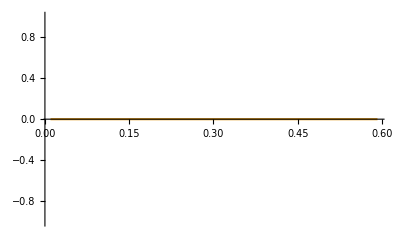

```mathematica
Plot[{Re[po[r]],Im[po[r]]},{r,r0,rStop},PlotRange->All]
```

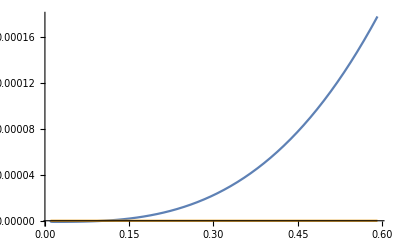

```mathematica
Plot[{Re[mo[r]/MSS],Im[mo[r]/MSS]},{r,r0,rStop},PlotRange->All]
```

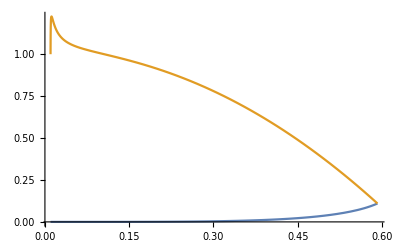

```mathematica
Plot[{Exp[nuo[r]],(1-(2 (GS/GSp) mo[r])/(r))},{r,r0,rStar}]
```

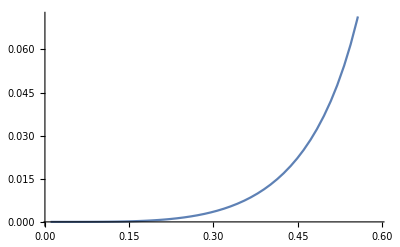

```mathematica
Plot[{Exp[nuo[r]]},{r,r0,rStar}]
```

```mathematica
(2 (GS/GSp) mo[r])/(r)/.{r->rStar}
```

0.890161

```mathematica
(2 (GS/GSp) mo[r])/(r)-N[8/9]/.{r->rStar}
```

0.00127238

HASIL SCGrav
alpha:=10.
lp:=10.^-3 

saat w=1/3 dan ϵ0=(4*(145)^4)/hbarc^3 dan PC=230 , hasilnya 2Compactness=0.531671<BL
saat w=1 dan ϵ0=(4*(145)^4)/hbarc^3 dan PC=230 , hasilnya 2Compactness=0.662569<BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 dan PC=230 , hasilnya 2Compactness=0.754262<BL


saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^9 dan PC=230*10^12 , hasilnya 2Compactness=0.888742<BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^9 dan PC=230*10^13 , hasilnya 2Compactness=0.888961>BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^9 dan PC=230*10^14 , hasilnya 2Compactness=0.890161>BL

saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^8 dan PC=230*10^14 , hasilnya 2Compactness=0.889297 >BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^7 dan PC=230*10^14 , hasilnya 2Compactness=0.889019>BL
saat w=Infinity dan ϵ0=(4*(145)^4)/hbarc^3 10^6 dan PC=230*10^14 , hasilnya 2Compactness=0.88893>BL

BL(Buchdahl limit) → 2 Compactness = 0.888889

```mathematica
tabel={{"l_p(m)","α","p_c(MeV fm^-3)","w","B(MeV^4)","2GM/R (SCGrav)","2GM/R (TOV GR)"},{0.001,10,230,"1/3","(145)^4",0.5316711272740902<BL,0.5286833358248435<BL},{0.001,10,230,1,"(145)^4",0.6625687801358684<BL,0.6586821174913947<BL},{0.001,10,230,Infinity,"(145)^4",0.7542622673492266<BL,0.74993<BL},{0.001,10,"230*10^12",Infinity,"(145)^4*10^9",0.8887418450301078<BL,0.888769<BL},{0.001,10,"230*10^13",Infinity,"(145)^4*10^9",0.8889606337207395>BL,0.888902>BL},{0.001,10,"230*10^14",Infinity,"(145)^4*10^9",0.8901612729078283>BL,0.888916>BL},{0.001,10,"230*10^14",Infinity,"(145)^4*10^8",0.8892974392401095>BL,0.8888915773915215>BL},{0.001,10,"230*10^14",Infinity,"(145)^4*10^7",0.8890189236183492>BL,0.8888891559881078+2.670992189646171*^-7>BL},{0.001,10,"230*10^14",Infinity,"(145)^4*10^6",0.8889301142513379>BL,0.8888889992745238+2.469954063499813*^-8>BL}};
Grid[tabel,Frame->All]
Export[FileNameJoin[{NotebookDirectory[],"tabel0.tex"}],%,"LaTeX"]
```

l_p(m) | α | p_c(MeV fm^-3) | w | B(MeV^4) | 2GM/R (SCGrav) | 2GM/R (TOV GR)
0.001 | 10 | 230 | 1/3 | (145)^4 | 0.531671<BL | 0.528683<BL
0.001 | 10 | 230 | 1 | (145)^4 | 0.662569<BL | 0.658682<BL
0.001 | 10 | 230 | ∞ | (145)^4 | 0.754262<BL | 0.74993<BL
0.001 | 10 | 230*10^12 | ∞ | (145)^4*10^9 | 0.888742<BL | 0.888769<BL
0.001 | 10 | 230*10^13 | ∞ | (145)^4*10^9 | 0.888961>BL | 0.888902>BL
0.001 | 10 | 230*10^14 | ∞ | (145)^4*10^9 | 0.890161>BL | 0.888916>BL
0.001 | 10 | 230*10^14 | ∞ | (145)^4*10^8 | 0.889297>BL | 0.888892>BL
0.001 | 10 | 230*10^14 | ∞ | (145)^4*10^7 | 0.889019>BL | 0.888889>BL
0.001 | 10 | 230*10^14 | ∞ | (145)^4*10^6 | 0.88893>BL | 0.888889>BL

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\tabel0.tex

```mathematica
(145)^4/197.327^3
```

57.5324

#### Run jika hasil numerik sudah benar memenuhi p[R]=0 dan m’[r]>0 untuk 0<r<R

```mathematica
filename=FileNameJoin[{NotebookDirectory[],"profil-vSCGrav_verif.dat"}]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\profil-vSCGrav_verif.dat

```mathematica
Export[filename,Table[{r/1,po[r]*10^-15,(mo[r]mp/MSS)*10^4,(1-(2 (GS/GSp) mo[r])/(r)),Exp[nuo[r]]},{r,r0,rStop,(rStop-r0)/1000}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\profil-vSCGrav_verif.dat

#### Lain hal, untuk bahas alpha<1 butuh EoS yg w<2/9

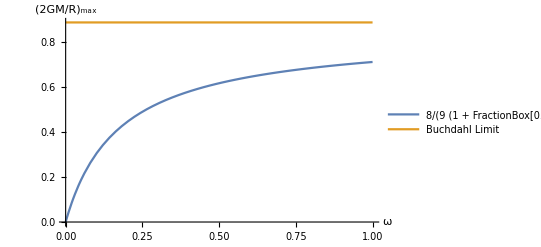

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\estimate.eps

```mathematica
Plot[{8/(9(1+(0.77+0.51 ω)/(ω(4.18+ω)))),8/9},{ω,0.,1.},AxesLabel->{"ω","(2GM/R)_max"},PlotLegends->{"8/(9 (1 + FractionBox[0.77 + 0.51 ω, ω (4.18 + ω)]))","Buchdahl Limit"}]
Export[FileNameJoin[{NotebookDirectory[],"estimate.eps"}],%]
```

```mathematica
8/(9(1+(0.77+0.51 ω)/(ω(4.18+ω))))/.{ω->2/9}
8/(9(1+(0.77+0.51 ω)/(ω(4.18+ω))))/.{ω->1/3}
8/(9(1+(0.77+0.51 ω)/(ω(4.18+ω))))/.{ω->1}
N[8/9]
```

0.46711

0.547071

0.712762

0.888889

#### Coba integrasi biar dapet r*

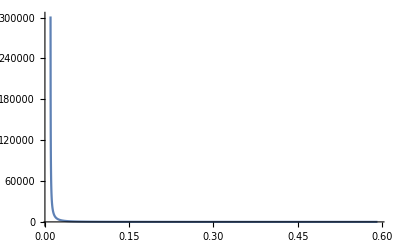

```mathematica
f[r_]:=1/(√(Exp[nuo[r]](1-(2 (GS/GSp) mo[r])/(r))))
Plot[f[r],{r,r0,rStar},PlotRange->All]
```

```mathematica
n:=1000
x[i_]:=r0+i/n(rStar-r0)
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"eksak-rstar.dat"}],Table[{x[j],rStar+2 GS mo[rStar] Log[rStar/(2 GS mo[rStar])-1]-Sum[(rStar-r0)/(2n)(f[x[i]]+f[x[i-1]]),{i,j,n}]},{j,1,n,1}]]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\variasi2\eksak-rstar.dat

```mathematica
datarstar=ReadList[FileNameJoin[{NotebookDirectory[],"eksak-rstar.dat"}],{Number,Number}];
```

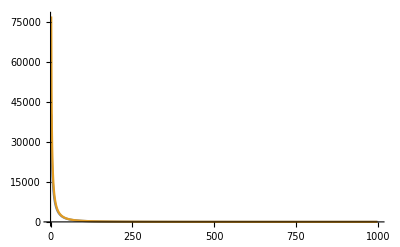

```mathematica
ListLinePlot[{Table[{j,f[datarstar[[j+1,1]]]},{j,2,n-1}],Table[{j,(datarstar[[j+1,2]]-datarstar[[j,2]])/(datarstar[[j+1,1]]-datarstar[[j,1]])},{j,2,n-1}]},PlotRange->All]
```

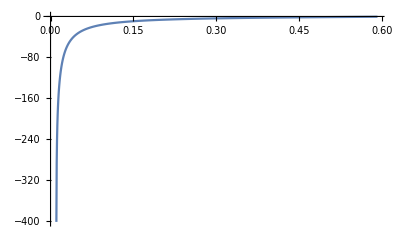

```mathematica
ListLinePlot[datarstar,PlotRange->All]
```